```mathematica
SetDirectory@NotebookDirectory[];
```

#### Potential and Hamiltonian

```mathematica
a=3;
b=-1;
V[q_]=a*q^2+b*q^3;
H[q_,p_,t_]=p^2/2+V[q];
```

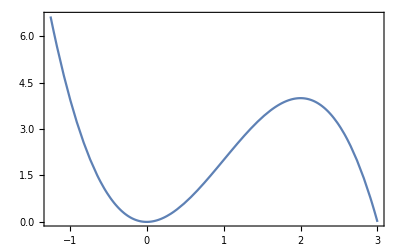

```mathematica
Plot[V[q],{q,-1.25,3},Frame->True,LabelStyle->{Black,18}]
```

```mathematica
(*Local maximum and minimum*)
sol=NSolve[D[V[q],q]==0,q];
xminloc=q/. sol[[1]]
xmaxloc=q/. sol[[2]]
V[xmaxloc]
```

0.

2.

4.

#### Classical phase space

```mathematica
(*H1*)
pin=0.0;
qin=xmaxloc-10^(-3);
tf=5000;
sol=NDSolve[{D[q[t],t]==D[H[q[t],p[t],t],p[t]],D[p[t],t]==-D[H[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
```

```mathematica
tint=0.1;
(*qp=Table[{q[t],p[t]}/.sol[[1]]/.t->i,{i,0,tf,tint}];*)
qpr=Table[{q[t],p[t]}/.sol[[1]]/.t->i,{i,0,tf,tint}];
```

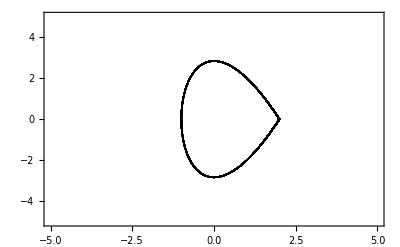

```mathematica
sep=ListPlot[{qpr},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-5,5},{-5,5}},LabelStyle->{16,Black}]
```

#### Wigner function

```mathematica
datawigner=Import["output/Wigner_MetastableState.dat"];
```

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

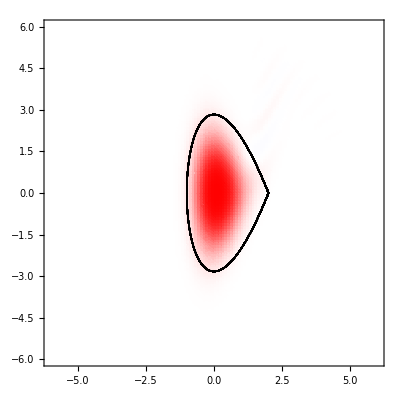

```mathematica
wigner=Show[ListDensityPlot[datawigner,PlotRange->{{-6,6},{-6,6},All},Frame->True,LabelStyle->{Black,24},ColorFunction->(FCo[1-0.5/0.35(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)],sep]
```